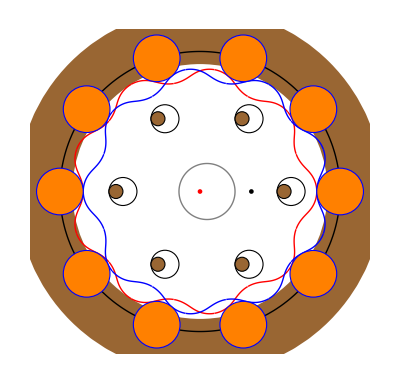

```mathematica
R=60;d=10;e=3;n=10;r=12;ro=36;nh=6;
ψ=-ArcTan[Sin[(1-n)*t]/((R/(e*n))-Cos[(1-n)*t])];
X[t_]:=R*Cos[t]-d*Cos[t-ψ]-e*Cos[n*t];
Y[t_]:=-R*Sin[t]+d*Sin[t-ψ]+e*Sin[n*t];
(*Modify the X function to flip it horizontally*)
Xf[t_]:=-R*Cos[t]+d*Cos[t-ψ]+e*Cos[n*t];
Yf[t_]:=-R*Sin[t]+d*Sin[t-ψ]+e*Sin[n*t];

rotorf[fi_]:=ParametricPlot[RotationMatrix[fi/9].{Xf[t],Yf[t]}+RotationMatrix[-fi].{-e,0},{t,0,2*Pi},PlotRange->All,AspectRatio->Automatic,PlotStyle->{Red,Thick},Axes->False,PlotPoints->110,Axes->True];
outputHolesf[fi_]:=Table[Graphics[{White,EdgeForm[Red],Disk[RotationMatrix[fi/9].({ro*Cos[2*Pi/nh*k],ro*Sin[2*Pi/nh*k]})+RotationMatrix[-fi].{-e,0},6]}],{k,1,nh}];

rotor[fi_]:=ParametricPlot[RotationMatrix[fi/9].{X[t],Y[t]}+RotationMatrix[-fi].{e,0},{t,0,2*Pi},PlotRange->All,AspectRatio->Automatic,PlotStyle->{Blue,Thick},Axes->False,PlotPoints->110,Axes->True];
(*Cycloidal Disk*)

rollers=Table[Graphics[{Orange,EdgeForm[Blue],Disk[{R*Cos[2*Pi/n*k],R*Sin[2*Pi/n*k]},d]}],{k,1,n}];
(*Orange circles*)

outputHoles[fi_]:=Table[Graphics[{White,EdgeForm[Black],Disk[RotationMatrix[fi/9].({ro*Cos[2*Pi/nh*k],ro*Sin[2*Pi/nh*k]})+RotationMatrix[-fi].{e,0},6]}],{k,1,nh}];
(*6 Blue circles*)

centerCircle[fi_]:=ParametricPlot[RotationMatrix[-fi].{r*Cos[t]+e,r*Sin[t]},{t,0,2*Pi},PlotStyle->{Gray,Thick}];
(*Blue center circle*)

center=Graphics[{Red,Disk[]}];
align=Graphics[Disk[{22,0},1]];

outputP[fi_]:=Table[Graphics[{Brown,EdgeForm[Black],Disk[RotationMatrix[fi/9].{ro*Cos[2*Pi/nh*k],ro*Sin[2*Pi/nh*k]},6-e]}],{k,1,nh}];
(*Brown outer circle*)

justAvisualContour=ParametricPlot[{R*Cos[t],R*Sin[t]},{t,0,2*Pi},PlotRange->All,AspectRatio->Automatic,Axes->True,PlotStyle->{Black,Thick}];
torus = Graphics[{Thickness[0.1],Brown,Circle[{0,0},66.5]},ImagePadding->All];
image =Show[torus,center,justAvisualContour,rotorf[0],rotor[0],rollers,(*outputHolesf[fi]*)outputHoles[0],centerCircle[0],outputP[0],align,Axes->False,Frame->False]
```

## Manipulate

```mathematica
Manipulate[Show[torus,center,justAvisualContour,rotorf[fi],rotor[fi],rollers,(*outputHolesf[fi]*)outputHoles[fi],centerCircle[fi],outputP[fi],Axes->False],{fi,0,9*2 Pi}]
```

## Export images

```mathematica
Export["C:\\Users\\vitok\\Desktop\\Cdsvg.svg",image,"SVG"]
```

C:\Users\vitok\Desktop\Cdsvg.svg